```mathematica
Record Input, save sound as s, save sampling rate as sr
```

```mathematica
s=SystemDialogInput["RecordSound"]
data=s[[1,1]];
sr=s[[1,2]];
Export["/tmp/a.wav",s];
```

-Graphics-

```mathematica
Normalize data, take filtered max, normalize again
```

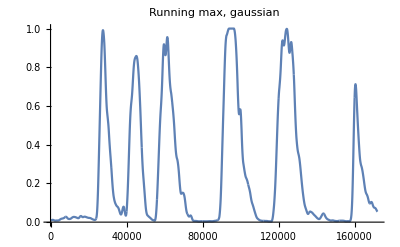

```mathematica
ndata=data/Max[Abs[data]];
avgdata=GaussianFilter[MaxFilter[ndata,410],1000];
navgdata=avgdata/Max[Abs[avgdata]];
ListLinePlot[navgdata,PlotRange->All,PlotLabel->"Running max, gaussian"]
```

## Try again with a highpass filter, find onsets

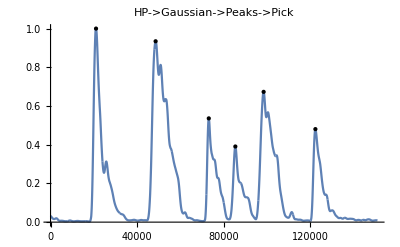

```mathematica
(*ndata=HighpassFilter[data/Max[Abs[data]],.8];*)
ndata=data/Max[Abs[data]];
avgdata=GaussianFilter[MaxFilter[ndata,410],1000];
navgdata=avgdata/Max[Abs[avgdata]];
pospeaks=FindPeaks[navgdata,0,0,-Infinity];
negpeaks=Map[({x,y}=#;{x,-y})&,FindPeaks[-navgdata,0 , 0, -Infinity]];
peaks=Union[pospeaks,negpeaks];
onsets=Reap[Do[
If[peaks[[i,2]]<0.1  &&  peaks[[i+1,2]]>0.1,
Sow[{peaks[[i+1,1]],peaks[[i+1,2]]}]],
{i,1,Length[peaks]-1}]][[2,1]];
ListLinePlot[navgdata,PlotRange->All,Epilog->{Point[onsets]},PlotLabel->"HP->Gaussian->Peaks->Pick"]
```

## Show envelope on top of original signal

```mathematica
Show[{ListLinePlot[ndata,PlotStyle->{Blue},PlotRange->All],
         ListLinePlot[navgdata,PlotStyle->{Purple},PlotRange->All]},
         PlotRange->All,GridLines->{First/@onsets,{}}]
First/@onsets
```

-Graphics-

{20232,50195,80504,100010,116206,152108}

## Render snare on top of original audio, export to Python

```mathematica
notes=SoundNote["Snare",{#/sr-.2,#/sr+.5-.2}]&/@(First/@onsets);
Sound[Join[notes,{s}]]
Export["/tmp/seqinput.txt",N/@Join[{Length[data]},First/@onsets]];
```

Transpose::nmtx: The first two levels of {{{{0.276528,38},{0.900754,38},{1.45784,38},{1.73608,38},{2.03244,38},{2.57466,38}}},{{{0.00500504,0}},{{0.776543,38},{1.40077,38},{1.95785,38},{2.23606,38},{2.53243,38},{3.07468,38}}}} cannot be transposed.

-Graphics-